```mathematica
(a b)^2/(a^2+b^2)
```

(a^2 b^2)/(a^2+b^2)

```mathematica
%/.a->1/A/.b->1/B
```

1/(A^2 (1/A^2+1/B^2) B^2)

```mathematica
%//FullSimplify
```

1/(A^2+B^2)

```mathematica
1/%
```

A^2+B^2

```mathematica
th=ArcTan[.357/.652]
```

0.500957

```mathematica
.357Cos[th] (*EM*)
```

0.313133

```mathematica
4Pi/%^2(*alphaEM*)
```

128.16

```mathematica
.357Sin[th](*Z EM*)
```

0.171455

```mathematica
1/(1/.357^2+1/.652^2)
```

0.0980523

```mathematica
.313^2
```

0.097969

```mathematica
.357/Sin[th](*Z NC*)
```

0.743339

```mathematica
1/1.221
```

0.819001

```mathematica
1/.1715
```

5.8309

```mathematica
1.221/.1715
```

7.11953

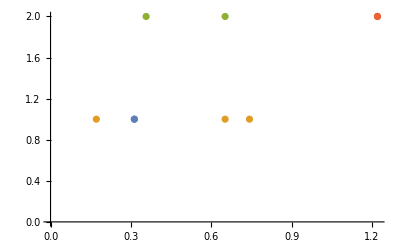

```mathematica
ListPlot[{{{.313,1}},{#,1}&/@{.171,.743,.652},{#,2}&/@{.357,.652},{{1.221,2}}}]
```